```mathematica
Q[x_]:=1/2 Erfc[x/Sqrt[2]]
```

```mathematica
rew =h * p1 * Q[η-Abs[μ]]- (1-p1) *  Q[η];
```

## When both threshold and d prime are free parameters and no cost for d prime Sol: Degenerate? Extremely high eta and even super high mu?

```mathematica
Manipulate[Plot[{((p1 * Q[η-Abs[μ]])/.{p1-> p1tmp})/.{NMaximize[rew/.{p1-> p1tmp},{η,μ}][[2]]},(((1-p1) *  Q[η])/.{p1-> p1tmp})/.{NMaximize[rew/.{p1-> p1tmp},{η,μ}][[2]]}},{h,0.01,2},PlotLegends->{"Hit","FA"},AxesLabel->{"Food reward"}, PlotRange->All],{{p1tmp,0.5},0,1},{{μtmp,1},0,10}]
```

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{((h * p1 * Q[η-Abs[μ]])/.{p1-> p1tmp})/.{NMaximize[rew/.{p1-> p1tmp},{η,μ}][[2]]},(((1-p1) *  Q[η])/.{p1-> p1tmp})/.{NMaximize[rew/.{p1-> p1tmp},{η,μ}][[2]]},((h * p1 * Q[η-Abs[μ]]- (1-p1) *  Q[η])/.{p1-> p1tmp})/.{NMaximize[rew/.{p1-> p1tmp},{η,μ}][[2]]}},{h,0.01,2},PlotLegends->{"Hit reward","FA cost", "Total reward"},AxesLabel->{"Food reward"}, PlotRange->All],{{p1tmp,0.5},0,1},{{μtmp,1},0,10}]
```

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

ReplaceAll::reps: {η,μ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMaximize::nnum: The function value -rew is not a number at {η,μ} = {0.918621,0.716689}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{η/.{NMaximize[rew/.{p1-> p1tmp},{η,μ}][[2]]},μ/.{NMaximize[rew/.{p1-> p1tmp},{η,μ}][[2]]}},{h,0.01,2},PlotLegends->{"Hit","FA"},AxesLabel->{"Food reward"}, PlotRange->All],{{p1tmp,0.5},0,1},{{μtmp,1},0,10}]
```

## When only threshold is a free parameters and no cost for d prime Sol: reduce threshold with increasing food reward

```mathematica
Manipulate[Plot[{((p1 * Q[η-Abs[μ]])/.{p1-> p1tmp, μ-> μtmp})/.{NMaximize[rew/.{p1-> p1tmp, μ-> μtmp},{η}][[2]]},(((1-p1) *  Q[η])/.{p1-> p1tmp, μ-> μtmp})/.{NMaximize[rew/.{p1-> p1tmp, μ-> μtmp},{η}][[2]]}},{h,0.01,2},PlotLegends->{"Hit","FA"},AxesLabel->{"Food reward"}, PlotRange->All],{{p1tmp,0.5},0,1},{{μtmp,1},0,10}]
```

```mathematica
Manipulate[Plot[{((h * p1 * Q[η-Abs[μ]])/.{p1-> p1tmp, μ-> μtmp})/.{NMaximize[rew/.{p1-> p1tmp, μ-> μtmp},{η}][[2]]},(((1-p1) *  Q[η])/.{p1-> p1tmp, μ-> μtmp})/.{NMaximize[rew/.{p1-> p1tmp, μ-> μtmp},{η}][[2]]},((h * p1 * Q[η-Abs[μ]]- (1-p1) *  Q[η])/.{p1-> p1tmp, μ-> μtmp})/.{NMaximize[rew/.{p1-> p1tmp, μ-> μtmp},{η}][[2]]}},{h,0.01,2},PlotLegends->{"Hit reward","FA cost", "Total reward"},AxesLabel->{"Food reward"}, PlotRange->All],{{p1tmp,0.5},0,1},{{μtmp,1},0,10}]
```

```mathematica
Manipulate[Plot[{η/.{NMaximize[rew/.{p1-> p1tmp, μ-> μtmp},{η}][[2]]}},{h,0.01,10},PlotLegends->{"Hit","FA"},AxesLabel->{"Food reward"}, PlotRange->All],{{p1tmp,0.5},0,1},{{μtmp,1},0,10}]
```

```mathematica
rew
```

-0.2 Erfc[η/(√2)]+0.3 h Erfc[(η-Abs[μ])/(√2)]

```mathematica
rew =h * p1 * Q[η-Abs[μ]]- (1-p1) *  Q[η];
```

```mathematica
Solve[D[rew,η]==0,η]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→Abs[μ]/2+Log[-(-1+p1)/(h p1)]/Abs[μ]}}

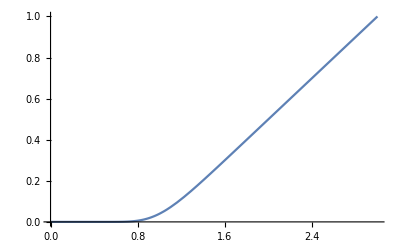

```mathematica
Plot[rew/.{η->Abs[μ]/2+Log[-(-1+p1)/(h p1)]/Abs[μ]}/.{p1->.5,μ->.2},{h,0,3}]
```

```mathematica
Manipulate[Plot[{Q[η]/.{η->Abs[μ]/2+Log[-(-1+p1)/(h p1)]/Abs[μ]}/.{p1->.5,μ->μtmp},Q[η-Abs[μ]]/.{η->Abs[μ]/2+Log[-(-1+p1)/(h p1)]/Abs[μ]}/.{p1->.5,μ->μtmp}},{h,0,10},AxesLabel->{"food reward","false alarm"},PlotRange->{0,1},PlotLegends->{"FA prob.","hit prob."}],{{μtmp,.2},0.0001,2}]
```

```mathematica
Manipulate[Plot[(Q[η-Abs[μ]]-Q[η])/.{η->Abs[μ]/2+Log[-(-1+p1)/(h p1)]/Abs[μ]}/.{p1->.5,μ->μtmp},{h,0,10},AxesLabel->{"food reward","false alarm"},PlotRange->{0,1},PlotLegends->{"FA prob.","hit prob."}],{{μtmp,.2},0.0001,2}]
```